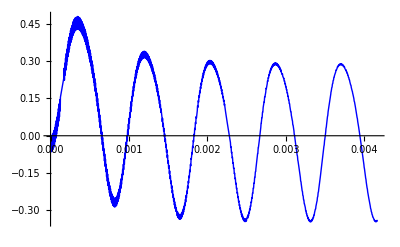

```mathematica
R1=10000;
R2=22000;
R3=33000;
C1=56*10^-9;
C2=47 *10^-9; 
L=82 *10^-6; 

amplitudaU=5; 
frekvenceU=1200;
amplitudaI=0.100;
frekvenceI=2400;

uZ[t]=amplitudaU*(Sin[2*Pi*frekvenceU*t])/2;
iZ[t]=amplitudaI*(Sin[2*Pi*frekvenceI*t])/2; 

uzel1=iU[t]==iR1[t];
uzel2=iR1[t]+iZ[t]==iR2[t]+iC1[t]+iL[t];
uzel3=iL[t]==iZ[t]+iR3[t]+iC2[t];

rez1=u1[t]-u2[t]==iR1[t]*R1;
rez2=u2[t]==iR2[t]*R2;
rez3=u3[t]==iR3[t]*R3;
cond1=iC1[t]==C1*u2'[t];
cond2=iC2[t]==C2*u3'[t];
ind=u2[t]-u3[t]==L*iL'[t];
zdroj=uZ[t]==u1[t];
podm1=u2[0]==0;
podm2=u3[0]==0;
podm3=iL[0]==0;

rovnice={uzel1,uzel2,uzel3,rez1,rez2,rez3,cond1,cond2,ind,zdroj,podm1,podm2,podm3};
nezname={iU[t],iR1[t],iR2[t],iR3[t],iC1[t],iC2[t],iL[t],u1[t],u2[t],u3[t]};
vysledek=NDSolve[rovnice,nezname,{t,0,5*1/frekvenceU},StartingStepSize->10^-20,MaxSteps->10000000];

Plot[{u3[t]/.vysledek},{t,0,5*1/frekvenceU},PlotStyle->{{Blue,Thick}}]
```